CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\" already exists.

CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\sort\\" already exists.

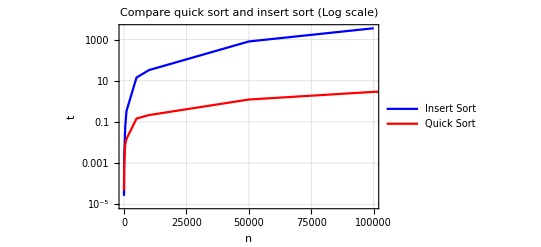

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

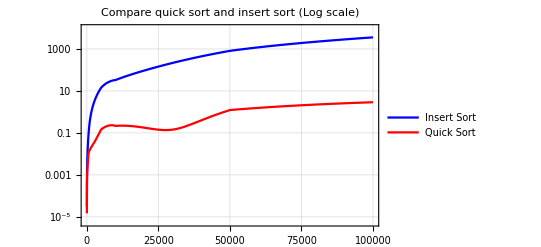

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

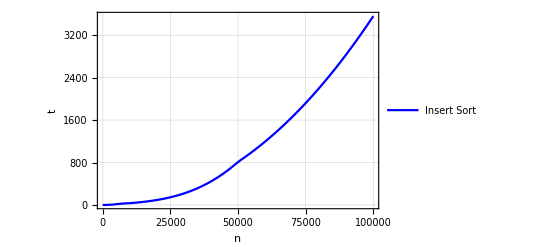

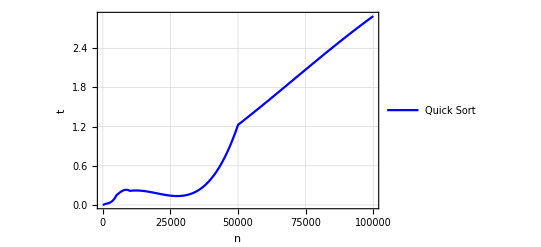

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = CreateDirectory["shown results"];
SetDirectory[workingDirectory];
file= OpenRead["../log_sort.txt"];
workingDirectory = CreateDirectory["sort"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];
quickSortResults = filelist[[2;;;;3]];
insertSortResults = filelist[[1;;;;3]];
insertSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,insertSortResults][[;;-4]];
quickSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,quickSortResults];
insertSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,insertSortResults];
quickSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,quickSortResults];
Plot1 = Show[ListLogPlot[insertSortResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Insert Sort"},PlotLabel->"Compare quick sort and insert sort (Log scale)", AxesLabel->{"n","t"},PlotTheme->"Detailed"],ListLogPlot[quickSortResults,Joined->True,PlotStyle->Red,PlotLegends->{"Quick Sort"}]]
insertFunc = Interpolation[insertSortResults];
quickFunc = Interpolation[quickSortResults];
Plot2 = LogPlot[{insertFunc[x],quickFunc[x]},{x,0,10^5},PlotStyle->{Blue,Red},PlotLegends->{"Insert Sort","Quick Sort"},PlotLabel->"Compare quick sort and insert sort (Log scale)",PlotTheme->"Detailed"]
Plot3 = Plot[insertFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Insert Sort"},AxesLabel->{"n","t"},PlotTheme->"Detailed"]
Plot4 = Plot[quickFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Quick Sort"},AxesLabel->{"n","t"},PlotTheme->"Detailed"]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Insert.gif",Plot3,ImageSize->2048];
Export["Quick.gif",Plot4,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Time"},quickSortResults[[All,1]]],Join[{"Insert sort"},insertSortResults[[All,2]],{"-","-","-"}],Join[{"Quick sort"},quickSortResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Time | Insert sort | Quick sort
5 | 0.0000256593 | 0.0000483861
10 | 0.0000447205 | 0.0000975053
50 | 0.000838692 | 0.000503289
100 | 0.00245339 | 0.000984217
500 | 0.0592224 | 0.0082381
1000 | 0.340541 | 0.0150154
5000 | 14.3163 | 0.145716
10000 | 32.9832 | 0.215359
50000 | 811.577 | 1.22726
100000 | 3560.33 | 2.89332
500000 | - | 23.6987
1000000 | - | 53.1463
5000000 | - | 286.583

```mathematica
Export["TableSort.gif",grid,ImageSize->{2048,720}];
Export["TableSort.xls",grid,ImageSize->{2048,720}];
```